```mathematica
Manipulate[Style["Hello",c],{c,{Red,Blue,Green}}]
```

```mathematica
CurrentImage[]
```

-Graphics-

```mathematica
Import["ExampleData/spikey.tiff"]
```

-Graphics-

```mathematica
Image3D[RandomReal[1,{5,10,10}]]
```

-Graphics3D-

```mathematica
Image3D[RandomReal[1,{5,10,10,3}]]
```

-Graphics3D-

```mathematica
Import["ExampleData/CTengine.tiff","Image3D"]
```

-Graphics3D-

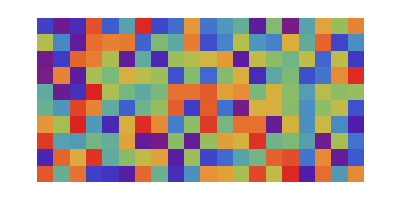

```mathematica
ArrayPlot[RandomReal[1,{10,20}],ColorFunction->"Rainbow"]
```

```mathematica
Image3D[#,ImageSize->150]&/@CellularAutomaton[{14,{2,1},{1,1,1}},{{{{1}}},0},8]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Manipulate[Image3D[CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{SeedRandom[n];RandomInteger[1,{15,15}],0},50]],{n,1,10}]
```

```mathematica
Manipulate[Image3D[CellularAutomaton[{52212111133224,{3,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{SeedRandom[n];RandomInteger[1,{15,15}],0},150],ImageSize->100],{n,1,10,1}]
```

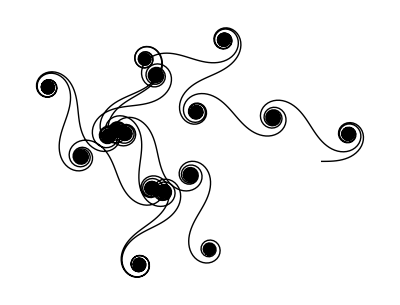

```mathematica
Graphics[Line[AnglePath[Range[0,100,.01]]]]
```

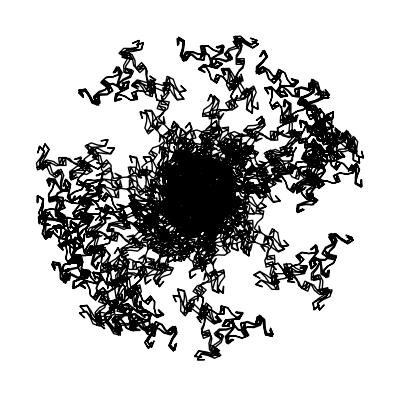

```mathematica
Graphics[Line[AnglePath[N[Range[10000]]]]]
```

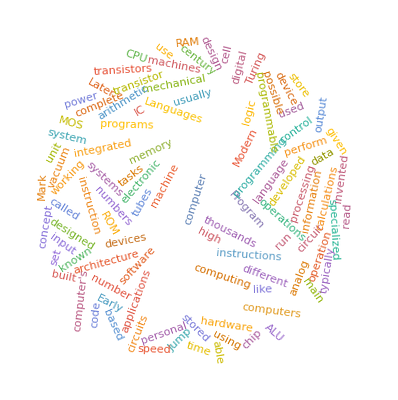

```mathematica
WordCloud[WikipediaData["Computer"],WordOrientation->"Random"]
```

```mathematica
ListPlot3D[GeoElevationData[GeoDisk[Entity["Mountain","MountEverest"],Quantity[2,"Miles"]]]]
```

-Graphics3D-

```mathematica
NestList[Join[{0},#]+Join[#,{0}]&,{1},8]
```

{{1},{1,1},{1,2,1},{1,3,3,1},{1,4,6,4,1},{1,5,10,10,5,1},{1,6,15,20,15,6,1},{1,7,21,35,35,21,7,1},{1,8,28,56,70,56,28,8,1}}

```mathematica
NestList[Join[{0},#]&,{1},8]//Grid
```

1 |  |  |  |  |  |  |  | 
0 | 1 |  |  |  |  |  |  | 
0 | 0 | 1 |  |  |  |  |  | 
0 | 0 | 0 | 1 |  |  |  |  | 
0 | 0 | 0 | 0 | 1 |  |  |  | 
0 | 0 | 0 | 0 | 0 | 1 |  |  | 
0 | 0 | 0 | 0 | 0 | 0 | 1 |  | 
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1

```mathematica
NestList[Join[#,{0}]&,{1},8]//Grid
```

1 |  |  |  |  |  |  |  | 
1 | 0 |  |  |  |  |  |  | 
1 | 0 | 0 |  |  |  |  |  | 
1 | 0 | 0 | 0 |  |  |  |  | 
1 | 0 | 0 | 0 | 0 |  |  |  | 
1 | 0 | 0 | 0 | 0 | 0 |  |  | 
1 | 0 | 0 | 0 | 0 | 0 | 0 |  | 
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
NestList[Join[{0},#]+Join[#,{0}]&,{1},8]
```

{{1},{1,1},{1,2,1},{1,3,3,1},{1,4,6,4,1},{1,5,10,10,5,1},{1,6,15,20,15,6,1},{1,7,21,35,35,21,7,1},{1,8,28,56,70,56,28,8,1}}

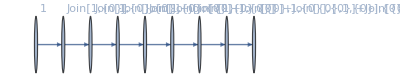

```mathematica
NestGraph[Join[{0},#]+Join[#,{0}]&,{1},8,VertexLabels->All]
```

```mathematica
NestList[{f[#],g[#]}&,x,3]
```

{x,{f[x],g[x]},{f[{f[x],g[x]}],g[{f[x],g[x]}]},{f[{f[{f[x],g[x]}],g[{f[x],g[x]}]}],g[{f[{f[x],g[x]}],g[{f[x],g[x]}]}]}}

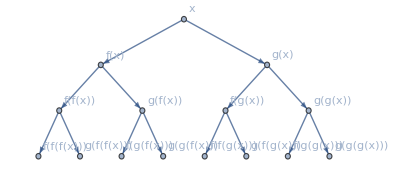

```mathematica
NestGraph[{f[#],g[#]}&,x,3,VertexLabels->All]
```

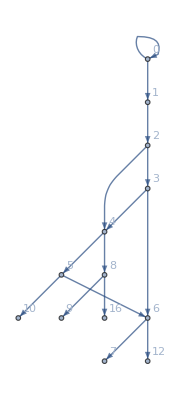

```mathematica
NestGraph[{#+1,2#}&,0,5,VertexLabels->All]
```

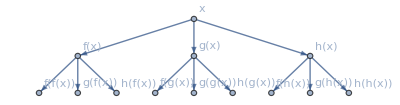

Syntax::sntxb: Expression cannot begin with "[#1*#2]&".

Array::argbu: Array called with 1 argument; between 2 and 4 arguments are expected.

```mathematica
NestGraph[{f[#],g[#],h[#]}&,x,2,VertexLabels->All]
```

```mathematica
Array[#1*#2&,{5,5}]//Grid
```

1 | 2 | 3 | 4 | 5
2 | 4 | 6 | 8 | 10
3 | 6 | 9 | 12 | 15
4 | 8 | 12 | 16 | 20
5 | 10 | 15 | 20 | 25

```mathematica
Array[If[#1==#2,x,#1*#2]&,{5,5}]//Grid
```

x | 2 | 3 | 4 | 5
2 | x | 6 | 8 | 10
3 | 6 | x | 12 | 15
4 | 8 | 12 | x | 20
5 | 10 | 15 | 20 | x

```mathematica
CommunityGraphPlot[RandomGraph[{100,200}]]
```

-Graphics-

WordList::nodict: Word list is not available for language ChineseSimplified.